```mathematica
Integrate[Exp[-(x-u)^2/2t],{x,-Infinity,0}]/(√(2π t))
```

ConditionalExpression[Erfc[(√t u)/(√2)]/(2 t),(Re[t]≥0&&Re[t u]>0)||Re[t]>0]

```mathematica
FullSimplify[Erfc[(√t u)/(√2)]/(2 t)]
```

Erfc[(√t u)/(√2)]/(2 t)

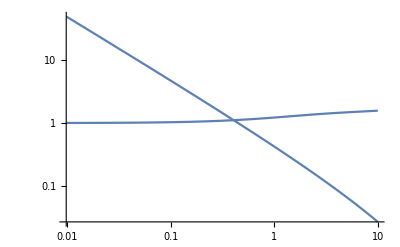

```mathematica
LogLogPlot[{Erfc[(√t (2p-1))/(√2)]/(2 t),}/.{p->0.6},{t,0,10}]
```

```mathematica
Sum[(1-p)^t(p/(1-p))^((t+b-x0)/2)Binomial[t,(t+b-x0)/2],{x0,b-t,b,2}]
```

1/p(p/(1-p))^(t-Floor[t/2]) ((-1+1/p)^t p (p/(1-p))^Floor[t/2]+(1-p)^t (-1+p) Binomial[t,-1+t-Floor[t/2]] Hypergeometric2F1[1,1-t+Floor[t/2],2+Floor[t/2],(-1+p)/p])

```mathematica
FullSimplify[%]
```

1/p(-p/(-1+p))^t ((-1+1/p)^t p+(1-p)^t (-1+p) (-p/(-1+p))^(-Floor[t/2]) Binomial[t,-1+t-Floor[t/2]] Hypergeometric2F1[1,1-t+Floor[t/2],2+Floor[t/2],(-1+p)/p])

```mathematica
P[t_,b_,p_]:=1/p(-p/(-1+p))^t ((-1+1/p)^t p+(1-p)^t (-1+p) (-p/(-1+p))^(-Floor[t/2]) Binomial[t,-1+t-Floor[t/2]] Hypergeometric2F1[1,1-t+Floor[t/2],2+Floor[t/2],(-1+p)/p])
```

```mathematica
LogLogPlot[P[t,0,0.6],{t,100,200}]
```

```mathematica
P0[x_,t_,p_]:=Sum[Binomial[t,m] p^m(1-p)^(t-m)KroneckerDelta[2m,t+x],{m,0,t}]
P1[x_,t_,p_]:=Piecewise[{{(1-p)^t Binomial[t,(t+x)/2](p/(1-p))^((t+x)/2),Mod[x,2]==0},{0,Mod[x,2]==1}}]
P2[x_,t_,p_]:=Piecewise[{{2/(√(2π t))Exp[(-(x-(2p-1)t)^2)/(2 t)],Mod[x,2]==0},{0,Mod[x,2]==1}}]
```

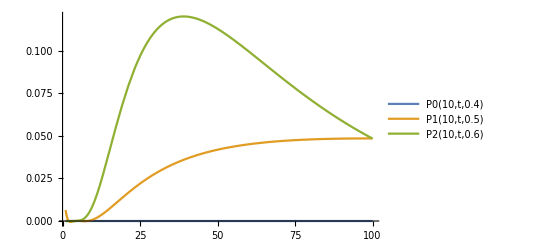

```mathematica
Plot[{P0[10,t,0.4],P1[10,t,0.5],P2[10,t,0.6]},{t,1,100},PlotRange->All,PlotLegends->LineLegend["Expressions",LabelStyle->{Gray,Bold,18}]]
```

```mathematica
Sum[P0[x,t,p],{x,0,t}]
```

```mathematica
P1[x_,t_,p_]:=Piecewise[{{(1-p)^t Binomial[t,(t+x)/2](p/(1-p))^((t+x)/2),Mod[x,2]==0},{0,Mod[x,2]==1}}]
Q1[t_,b_,p_]:=Sum[(P0[b-x0,t,p]-Sum[P0[b-x0,t0,p]P0[0,t-t0,p],{t0,1,t-1}]),{x0,b-t,b-1}]
DiscretePlot[Q1[t,10,0.6],{t,1,20}]
```

```mathematica
Q1[4,2,0.6]
```

-0.0568814

```mathematica
HeavisideTheta
```

```mathematica
DSolveValue[{D[P[x,t],t]==v D[P[x,t],{x,2}],P[x,0]==DiracDelta[x]},P[x,t],{x,t}]
```

(ⅇ^(-x^2/(4 t v)))/(2 √π √(t v))

```mathematica
Po[x_,t_]:=(ⅇ^(-(x)^2/(4 d t)))/(√(4π d t))
```

```mathematica
Integrate[(Po[x-(x1+u t),t]-Po[2 (b -(x1+u t))-(x-(x1+u t)),t])/T,{x1,b-T,b},Assumptions->{t>0,T>0,d>0}]//Simplify
```

(-Erf[(b+T-t u-x)/(2 √(d t))]+Erf[(b+t u-x)/(2 √(d t))]+Erf[(-b+T-t u+x)/(2 √(d t))]-Erf[(-b+t u+x)/(2 √(d t))])/(2 T)

```mathematica
Pa[x_,t_]:=(-Erf[(b+T-t u-x)/(2 √(d t))]+Erf[(b+t u-x)/(2 √(d t))]+Erf[(-b+T-t u+x)/(2 √(d t))]-Erf[(-b+t u+x)/(2 √(d t))])/(2 T)
-D[Pa[x,t],t]//FullSimplify
```

-1/(4 √π (d t)^(3/2) T)d (ⅇ^(-(-b+T-t u+x)^2/(4 d t)) (b-T-t u-x)-ⅇ^(-(-b+t u+x)^2/(4 d t)) (b+t u-x)+ⅇ^(-(b+T-t u-x)^2/(4 d t)) (b+T+t u-x)+ⅇ^(-(b+t u-x)^2/(4 d t)) (-b+t u+x))

```mathematica
Integrate[-1/(4 √π (d t)^(3/2) T)d (ⅇ^(-(-b+T-t u+x)^2/(4 d t)) (b-T-t u-x)-ⅇ^(-(-b+t u+x)^2/(4 d t)) (b+t u-x)+ⅇ^(-(b+T-t u-x)^2/(4 d t)) (b+T+t u-x)+ⅇ^(-(b+t u-x)^2/(4 d t)) (-b+t u+x)),x]//Simplify
```

-1/(2 √π √(d t) T)√d (√d ⅇ^(-(b+T-t u-x)^2/(4 d t))-√d ⅇ^(-(b+t u-x)^2/(4 d t))+√d ⅇ^(-(-b+T-t u+x)^2/(4 d t))-√d ⅇ^(-(-b+t u+x)^2/(4 d t))-√π √t u Erf[(b+T-t u-x)/(2 √d √t)]-√π √t u Erf[(b+t u-x)/(2 √d √t)]-√π √t u Erf[(-b+T-t u+x)/(2 √d √t)]-√π √t u Erf[(-b+t u+x)/(2 √d √t)])

```mathematica
Simplify[%,Assumptions->{b>0,0<t<T,d>0}]
```

-1/(2 √π √t T)(√d ⅇ^(-(b+T-t u-x)^2/(4 d t))-√d ⅇ^(-(b+t u-x)^2/(4 d t))+√d ⅇ^(-(-b+T-t u+x)^2/(4 d t))-√d ⅇ^(-(-b+t u+x)^2/(4 d t))-√π √t u Erf[(b+T-t u-x)/(2 √(d t))]-√π √t u Erf[(b+t u-x)/(2 √(d t))]-√π √t u Erf[(-b+T-t u+x)/(2 √(d t))]-√π √t u Erf[(-b+t u+x)/(2 √(d t))])

```mathematica
%/.x->b
```

-(-2 √d ⅇ^(-(t u^2)/(4 d))+2 √d ⅇ^(-(T-t u)^2/(4 d t))-2 √π √t u Erf[(t u)/(2 √(d t))]-2 √π √t u Erf[(T-t u)/(2 √(d t))])/(2 √π √t T)

```mathematica
(-2 √d ⅇ^(-(t u^2)/(4 d))+2 √d ⅇ^(-(T-t u)^2/(4 d t))-2 √π √t u Erf[(t u)/(2 √(d t))]-2 √π √t u Erf[(T-t u)/(2 √(d t))])/(2 √π √t T)//FullSimplify
```

((√d (-ⅇ^(-(t u^2)/(4 d))+ⅇ^(-(T-t u)^2/(4 d t))))/(√π √t)-u (Erf[(t u)/(2 √(d t))]+Erf[(T-t u)/(2 √(d t))]))/T

```mathematica
1/T((√d)/(√π √t)(-ⅇ^(-(t u^2)/(4 d))+ⅇ^(-(T-t u)^2/(4 d t)))-u (Erf[(t u)/(2 √(d t))]+Erf[(T-t u)/(2 √(d t))]))==
((d (ⅇ^(-(t u^2)/(4 d))-ⅇ^(-(T-t u)^2/(4 d t))))/(√π √(d t))+u (Erf[(t u)/(2 √(d t))]+Erf[(T-t u)/(2 √(d t))]))/T//Simplify
```

(ⅇ^(-(T^2+t^2 u^2)/(4 d t)) (ⅇ^(T^2/(4 d t))-ⅇ^((T u)/(2 d))) (√d √t-√(d t)))/(√t T)==0

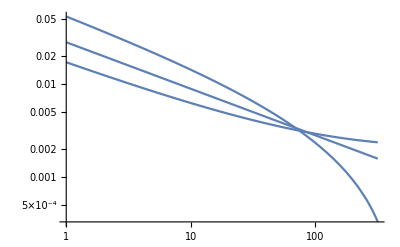

```mathematica
F[t_,u_,T_]:=(1/(2 √(2 π) √t)+u)/((√T)/(√(2 π))+T u) (*approx, for u≥0*)
F1[t_,u1_,T_]:=Table[Piecewise[{{(1/(2 √(2 π) √t)+u)/((1+2 √(1/u^2) u)/(8 π u)),u<0},{(1/(2 √(2 π) √t)+u)/((√T)/(√(2 π))+T u),u≥ 0}}],{u,u1}]
F2[t_,u_,T_,d_]:=(u*Erf[(t*u)/(2*Sqrt[d*t])] + ((E^(-((t*u^2)/(4*d))) - E^(-((T - t*u)^2/(4*d*t))))*
       Sqrt[d*t] + Sqrt[Pi]*t*u*Erf[(T - t*u)/(2*Sqrt[d*t])])/(Sqrt[Pi]*t))/T/
  (1 + 2*Sqrt[d/(Pi*T)]*(-E^(-((T*(-1 + u)^2)/(4*d))) + E^(-((T*u^2)/(4*d)))) + 
   u*Erf[(T*u)/(2*Sqrt[d*T])] + (-1 + u)*Erf[(T - T*u)/(2*Sqrt[d*T])])(* exact result for u≥0*)
F3[t_,u_,T_]:=(1/(2 √(2 π) √t T)ⅇ^(-(T^2+t^2 u^2)/(2 t)) (1+T) (ⅇ^(T^2/(2 t))-ⅇ^(T u)+ⅇ^((T^2+t^2 u^2)/(2 t)) √(2 π) √t u Erf[(√t u)/(√2)]+ⅇ^((T^2+t^2 u^2)/(2 t)) √(2 π) √t u Erf[(T-t u)/(√2 √t)]))/(1/(2 √(2 π) T)(1+T) (-2 ⅇ^(-1/2 T (-1+u)^2) √T+2 ⅇ^(-(T u^2)/2) √T+√(2 π) T-ⅇ^(2 T u) √(2 π) T+√(2 π) T (-(-1+u) Erf[(√T (-1+u))/(√2)]+u Erf[(√T u)/(√2)]))+1/2 ⅇ^(2 T u) (1+T))(*Exact result for u<0*)
F4[t_,u_,T_]:=(√(2/π) (ⅇ^(-(t u^2)/2)-ⅇ^(-(T-t u)^2/(2 t))+√(2 π) √t u (Erf[(√t u)/(√2)]+Erf[(T-t u)/(√2 √t)])))/(√t T (2+(2 ⅇ^(-1/2 T (1+u^2)) (ⅇ^(T/2)-ⅇ^(T u)) √(2/π))/(√T)-2 (-1+u) Erf[(√T (-1+u))/(√2)]+2 u Erf[(√T u)/(√2)]))
LogLogPlot[{F2[t,{-0.04,0,0.04},320,1]},{t,1,320},PlotRange->All]
```

```mathematica
Integrate[1/(2 √(2 π) t^(3/2) T)(ⅇ^(-(b+t u-x)^2/(2 t)) T (b-t u-x)+ⅇ^(-(-b+t u+x)^2/(2 t)) (b+t u-x)-ⅇ^(-(b+T-t u-x)^2/(2 t)) (b+T+t u-x)+ⅇ^(-(-b+T-t u+x)^2/(2 t)) T (-b+T+t u+x)),x]
```

1/(2 √(2 π) t^(3/2) T)(-ⅇ^(-(b+T-t u-x)^2/(2 t)) t+ⅇ^(-(-b+t u+x)^2/(2 t)) t+ⅇ^(-(b+t u-x)^2/(2 t)) t T-ⅇ^(-(-b+T-t u+x)^2/(2 t)) t T+√(2 π) t^(3/2) u Erf[(b+T-t u-x)/(√2 √t)]+√(2 π) t^(3/2) T u Erf[(b+t u-x)/(√2 √t)]+√(2 π) t^(3/2) T u Erf[(-b+T-t u+x)/(√2 √t)]+√(2 π) t^(3/2) u Erf[(-b+t u+x)/(√2 √t)])

```mathematica
1/(2 √(2 π) t^(3/2) T)(-ⅇ^(-(b+T-t u-x)^2/(2 t)) t+ⅇ^(-(-b+t u+x)^2/(2 t)) t+ⅇ^(-(b+t u-x)^2/(2 t)) t T-ⅇ^(-(-b+T-t u+x)^2/(2 t)) t T+√(2 π) t^(3/2) u Erf[(b+T-t u-x)/(√2 √t)]+√(2 π) t^(3/2) T u Erf[(b+t u-x)/(√2 √t)]+√(2 π) t^(3/2) T u Erf[(-b+T-t u+x)/(√2 √t)]+√(2 π) t^(3/2) u Erf[(-b+t u+x)/(√2 √t)])/.x->b//Simplify
```

(ⅇ^(-(T^2+t^2 u^2)/(2 t)) (1+T) (ⅇ^(T^2/(2 t))-ⅇ^(T u)+ⅇ^((T^2+t^2 u^2)/(2 t)) √(2 π) √t u Erf[(√t u)/(√2)]+ⅇ^((T^2+t^2 u^2)/(2 t)) √(2 π) √t u Erf[(T-t u)/(√2 √t)]))/(2 √(2 π) √t T)

```mathematica
Integrate[(ⅇ^(-(T^2+t^2 u^2)/(2 t)) (1+T) (ⅇ^(T^2/(2 t))-ⅇ^(T u)+ⅇ^((T^2+t^2 u^2)/(2 t)) √(2 π) √t u Erf[(√t u)/(√2)]+ⅇ^((T^2+t^2 u^2)/(2 t)) √(2 π) √t u Erf[(T-t u)/(√2 √t)]))/(2 √(2 π) √t T),t]
```

1/(2 √(2 π) T)(1+T) (2 ⅇ^(-(t u^2)/2) √t-2 ⅇ^(-(T-t u)^2/(2 t)) √t+√(2 π) t u Erf[(√t u)/(√2)]+√(2 π) t u Erf[(T-t u)/(√2 √t)]+1/(√(T^2) √(u^2))ⅇ^(T u-√(T^2) √(u^2)) √(π/2) T ((√(T^2) u+T √(u^2)) Erf[(-√(T^2)+t √(u^2))/(√2 √t)]-(-√(T^2) u+T √(u^2)) (1-ⅇ^(2 √(T^2) √(u^2))+ⅇ^(2 √(T^2) √(u^2)) Erf[(√(T^2)+t √(u^2))/(√2 √t)])))

```mathematica
1/(2 √(2 π) T)(1+T) (2 ⅇ^(-(t u^2)/2) √t-2 ⅇ^(-(T-t u)^2/(2 t)) √t+√(2 π) t u Erf[(√t u)/(√2)]+√(2 π) t u Erf[(T-t u)/(√2 √t)]+1/(√(T^2) √(u^2))ⅇ^(T u-√(T^2) √(u^2)) √(π/2) T ((√(T^2) u+T √(u^2)) Erf[(-√(T^2)+t √(u^2))/(√2 √t)]-(-√(T^2) u+T √(u^2)) (1-ⅇ^(2 √(T^2) √(u^2))+ⅇ^(2 √(T^2) √(u^2)) Erf[(√(T^2)+t √(u^2))/(√2 √t)])))/.t->T
```

1/(2 √(2 π) T)(1+T) (2 ⅇ^(-(T u^2)/2) √T-2 ⅇ^(-(T-T u)^2/(2 T)) √T+√(2 π) T u Erf[(√T u)/(√2)]+√(2 π) T u Erf[(T-T u)/(√2 √T)]+1/(√(T^2) √(u^2))ⅇ^(T u-√(T^2) √(u^2)) √(π/2) T ((√(T^2) u+T √(u^2)) Erf[(-√(T^2)+T √(u^2))/(√2 √T)]-(-√(T^2) u+T √(u^2)) (1-ⅇ^(2 √(T^2) √(u^2))+ⅇ^(2 √(T^2) √(u^2)) Erf[(√(T^2)+T √(u^2))/(√2 √T)])))

```mathematica
FullSimplify[%,Assumptions->{T>0,u<0,Element[{T,u},Reals]}]
```

1/(2 √(2 π) T)(1+T) (-2 ⅇ^(-1/2 T (-1+u)^2) √T+2 ⅇ^(-(T u^2)/2) √T+√(2 π) T-ⅇ^(2 T u) √(2 π) T+√(2 π) T (-(-1+u) Erf[(√T (-1+u))/(√2)]+u Erf[(√T u)/(√2)]))

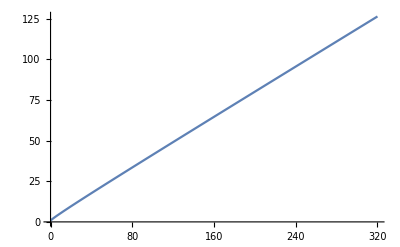

```mathematica
Plot[(1/(2 √(2 π) T)(1+T) (-2 ⅇ^(-1/2 T (-1+u)^2) √T+2 ⅇ^(-(T u^2)/2) √T+√(2 π) T-ⅇ^(2 T u) √(2 π) T+√(2 π) T (-(-1+u) Erf[(√T (-1+u))/(√2)]+u Erf[(√T u)/(√2)]))+1/2 (-1+ⅇ^(2 T u)+√π) (1+T))/.{u->-0.04},{T,0,320}]
```

```mathematica
1/(2 √(2 π) T)(1+T) (1/(-T u)ⅇ^(2T u) √(π/2) T (-(T u-T u) √π-(-T u-T u) (1-ⅇ^(-2 T u)+ⅇ^(- 2 T u) √π)))//FullSimplify
```

-1/2 (-1+ⅇ^(2 T u)+√π) (1+T)

```mathematica
{1/2 (-1+ⅇ^(2 T u)+√π) (1+T),1/(2 √(2 π) T)(1+T) (1/(-T u)ⅇ^(2T u) √(π/2) T 2T u)}/.{T->320,u->-0.04,t->0.1}
```

{123.979,-1.22331×10^-9}

```mathematica
ⅇ^(T u-√(T^2) √(u^2))/.{T->320,u->-0.04,t->0.00001}
```

7.62187×10^-12

```mathematica
{1/2 (-1+ⅇ^(2 T u)+√π) (1+T),1/(2 √(2 π) T)(1+T) (1/(-T u)ⅇ^(2T u) √(π/2) T 2T u)}//Simplify
```

{1/2 (-1+ⅇ^(2 T u)+√π) (1+T),-1/2 ⅇ^(2 T u) (1+T)}

```mathematica
Integrate[(ⅇ^(-(t u^2)/2))/(2 √(2 π) √t)+1/2 u Erf[(√t u)/(√2)]/.{T->3200,u->0.04},{t,0,320}]//N
```

8.88931

```mathematica
((ⅇ^(-(t u^2)/2)+√(2 π) √t u (Erf[(√t u)/(√2)]+Erf[(T-t u)/(√2 √t)]))/(2 √(2 π) √t))/(T/(2 √(2 π)) (√(2 π) (-1+u) Erf[(√T (-1+u))/(√2)]+√(2 π)  u Erf[(√T u)/(√2)])+(T)/2) //FullSimplify
```

(ⅇ^(-(t u^2)/2)+√(2 π) √t u (Erf[(√t u)/(√2)]+Erf[(T-t u)/(√2 √t)]))/(√(2 π) √t T (1+(-1+u) Erf[(√T (-1+u))/(√2)]+u Erf[(√T u)/(√2)]))

```mathematica
FullSimplify[(((1+T) (ⅇ^(-(t u^2)/2)-ⅇ^(-(T-t u)^2/(2 t))+√(2 π) √t u (Erf[(√t u)/(√2)]+Erf[(T-t u)/(√2 √t)])))/(2 √(2 π) √t T))/(1/(2 √(2 π) T)(1+T) (2 (-ⅇ^(-1/2 T (-1+u)^2)+ⅇ^(-(T u^2)/2)) √T-√(2 π) T (-1+u) Erf[(√T (-1+u))/(√2)]+√(2 π) T u Erf[(√T u)/(√2)])+(1+T)/2)]
```

(Sqrt[2/Pi]*(E^(-((t*u^2)/2)) - E^(-((T - t*u)^2/(2*t))) + 
    Sqrt[2*Pi]*Sqrt[t]*u*(Erf[(Sqrt[t]*u)/Sqrt[2]] + Erf[(T - t*u)/(Sqrt[2]*Sqrt[t])])))/
  (Sqrt[t]*T*(2 + (2*(E^(T/2) - E^(T*u))*Sqrt[2/Pi])/(E^((1/2)*T*(1 + u^2))*Sqrt[T]) - 
    2*(-1 + u)*Erf[(Sqrt[T]*(-1 + u))/Sqrt[2]] + 2*u*Erf[(Sqrt[T]*u)/Sqrt[2]]))

```mathematica
Erf[0.2]//N
```

0.222703

```mathematica
FullSimplify[Po[x-(x1+u t),t]-Po[2 (b -(x1+u t))-(x-(x1+u t)),t]]
```

(ⅇ^(-(t u-x+x1)^2/(4 d t))-ⅇ^(-(-2 b+t u+x+x1)^2/(4 d t)))/(2 √π √(d t))

```mathematica
Integrate[Po[x-(x1+u t),t]-Po[2 (b -(x1+u t))-(x-(x1+u t)),t]/T^2,{x1,b-T,b},Assumptions->{t>0,T>0,d>0}]//Simplify
```

1/2 (Erf[(b+t u-x)/(2 √(d t))]+Erf[(-b+T-t u+x)/(2 √(d t))]-(Erf[(b+T-t u-x)/(2 √(d t))]+Erf[(-b+t u+x)/(2 √(d t))])/T^2)

```mathematica
1/2 (Erf[(b+t u-x)/(2 √(d t))]+Erf[(-b+T-t u+x)/(2 √(d t))]-(Erf[(b+T-t u-x)/(2 √(d t))]+Erf[(-b+t u+x)/(2 √(d t))])/T^2)/.{t->t-t0}
```

1/2 (Erf[(b+(t-t0) u-x)/(2 √(d (t-t0)))]+Erf[(-b+T-(t-t0) u+x)/(2 √(d (t-t0)))]-(Erf[(b+T-(t-t0) u-x)/(2 √(d (t-t0)))]+Erf[(-b+(t-t0) u+x)/(2 √(d (t-t0)))])/T^2)

```mathematica
Simplify[(Po[x-(x1+u (t-t0)),(t-t0)]-Po[2 (b -(x1+u (t-t0)))-(x-(x1+u (t-t0))),(t-t0)])/T^2,Assumptions->{t>0,T>0,d>0}]
```

(ⅇ^(-(t u-t0 u-x+x1)^2/(4 d (t-t0)))-ⅇ^(-(-2 b+t u-t0 u+x+x1)^2/(4 d (t-t0))))/(2 √π T^2 √(d (t-t0)))

```mathematica
%//Simplify
```

```mathematica
Simplify[f[0],Assumptions->{0<t<T,x1<b,b>0,d>0,x<b,u>0}]
```

1/(2 T^2 u)ⅇ^(-(u (2 b+Abs[x-x1]))/(2 d)) (-ⅇ^((u (2 b+x-x1))/(2 d))+ⅇ^((u (2 b+Abs[x-x1]))/(2 d))-ⅇ^((u (6 b-2 (x+x1)+Abs[x-x1]))/(2 d))+ⅇ^((u (2 b+x-x1+2 Abs[x-x1]))/(2 d))+ⅇ^((u (6 b-2 (x+x1)+Abs[x-x1]))/(2 d)) Erf[(2 b+t u-x-x1)/(2 √(d t))]+ⅇ^((u (2 b+Abs[x-x1]))/(2 d)) Erf[(-2 b+t u+x+x1)/(2 √(d t))]-ⅇ^((u (2 b+x-x1))/(2 d)) Erf[(t u-Abs[x-x1])/(2 √(d t))]-ⅇ^((u (2 b+x-x1+2 Abs[x-x1]))/(2 d)) Erf[(t u+Abs[x-x1])/(2 √(d t))])

```mathematica
f[t0]
```

```mathematica
1/(2 T^2  √(u^2))ⅇ^(-(u (x+x1)+d √(u^2/d) (√((x-x1)^2/d)+√((-2 b+x+x1)^2/d)))/(2 d))  (ⅇ^((b u)/d+1/2 √(u^2/d) √((x-x1)^2/d))-ⅇ^((u x)/d+1/2 √(u^2/d) √((-2 b+x+x1)^2/d))+ⅇ^((u x)/d+1/2 √(u^2/d) (2 √((x-x1)^2/d)+√((-2 b+x+x1)^2/d)))-ⅇ^((b u)/d+1/2 √(u^2/d) (√((x-x1)^2/d)+2 √((-2 b+x+x1)^2/d)))-ⅇ^((u x)/d+1/2 √(u^2/d) (2 √((x-x1)^2/d)+√((-2 b+x+x1)^2/d))) -ⅇ^((u x)/d+1/2 √(u^2/d) √((-2 b+x+x1)^2/d)) (-1)+ⅇ^((b u)/d+1/2 √(u^2/d) (√((x-x1)^2/d)+2 √((-2 b+x+x1)^2/d))) +ⅇ^((b u)/d+1/2 √(u^2/d) √((x-x1)^2/d)) (-1))//Simplify
```

0

```mathematica
Limit[Erf[1/2 √(t-t0) (√((x-x1)^2/d))/(-t+t0)],t0->t]
```

```mathematica
Integrate[1/(2 T^2 u)ⅇ^(-(u (2 b+Abs[x-x1]))/(2 d)) (-ⅇ^((u (2 b+x-x1))/(2 d))+ⅇ^((u (2 b+Abs[x-x1]))/(2 d))-ⅇ^((u (6 b-2 (x+x1)+Abs[x-x1]))/(2 d))+ⅇ^((u (2 b+x-x1+2 Abs[x-x1]))/(2 d))+ⅇ^((u (6 b-2 (x+x1)+Abs[x-x1]))/(2 d)) Erf[(2 b+t u-x-x1)/(2 √(d t))]+ⅇ^((u (2 b+Abs[x-x1]))/(2 d)) Erf[(-2 b+t u+x+x1)/(2 √(d t))]-ⅇ^((u (2 b+x-x1))/(2 d)) Erf[(t u-Abs[x-x1])/(2 √(d t))]-ⅇ^((u (2 b+x-x1+2 Abs[x-x1]))/(2 d)) Erf[(t u+Abs[x-x1])/(2 √(d t))]),x1]
```

∫1/(2 T^2 u)ⅇ^(-(u (2 b+Abs[x-x1]))/(2 d)) (-ⅇ^((u (2 b+x-x1))/(2 d))+ⅇ^((u (2 b+Abs[x-x1]))/(2 d))-ⅇ^((u (6 b-2 (x+x1)+Abs[x-x1]))/(2 d))+ⅇ^((u (2 b+x-x1+2 Abs[x-x1]))/(2 d))+ⅇ^((u (6 b-2 (x+x1)+Abs[x-x1]))/(2 d)) Erf[(2 b+t u-x-x1)/(2 √(d t))]+ⅇ^((u (2 b+Abs[x-x1]))/(2 d)) Erf[(-2 b+t u+x+x1)/(2 √(d t))]-ⅇ^((u (2 b+x-x1))/(2 d)) Erf[(t u-Abs[x-x1])/(2 √(d t))]-ⅇ^((u (2 b+x-x1+2 Abs[x-x1]))/(2 d)) Erf[(t u+Abs[x-x1])/(2 √(d t))])ⅆx1

```mathematica
Integrate[(ⅇ^(-(t u-t0 u-x+x1)^2/(4 d (t-t0)))-ⅇ^(-(-2 b+t u-t0 u+x+x1)^2/(4 d (t-t0))))/(2 √π T^2 √(d (t-t0))),{x1,b-T,b},Assumptions->{0<t<T,t>t0,b>0,d>0,x<b}]
```

1/(2 T^2)(((b+t u-t0 u-x) Erf[1/2 √((b+t u-t0 u-x)^2/(d (t-t0)))])/(√((b+t u-t0 u-x)^2))+((b-t u+t0 u-x) Erf[1/2 √((b-t u+t0 u-x)^2/(d (t-t0)))])/(√((b-t u+t0 u-x)^2))-((b+T-t u+t0 u-x) Erf[1/2 √((b+T-t u+t0 u-x)^2/(d (t-t0)))])/(√((b+T-t u+t0 u-x)^2))-((b-T+t u-t0 u-x) Erf[1/2 √((-b+T-t u+t0 u+x)^2/(d (t-t0)))])/(√((-b+T-t u+t0 u+x)^2)))

```mathematica
Pa[x_,t_]:=(-Erf[(b+T-t u-x)/(2 √(d t))]+Erf[(b+t u-x)/(2 √(d t))]+Erf[(-b+T-t u+x)/(2 √(d t))]-Erf[(-b+t u+x)/(2 √(d t))])/(2 T)
Integrate[Pa[x,t],x]
```

(ⅇ^(-(b+T-t u-x)^2/(4 d t)) √(d t))/(√π T)-(ⅇ^(-(b+t u-x)^2/(4 d t)) √(d t))/(√π T)+(ⅇ^(-(-b+T-t u+x)^2/(4 d t)) √(d t))/(√π T)-(ⅇ^(-(-b+t u+x)^2/(4 d t)) √(d t))/(√π T)+((b+T-t u-x) Erf[(b+T-t u-x)/(2 √(d t))])/(2 T)-((b+t u-x) Erf[(b+t u-x)/(2 √(d t))])/(2 T)+((-b+T-t u+x) Erf[(-b+T-t u+x)/(2 √(d t))])/(2 T)-((-b+t u+x) Erf[(-b+t u+x)/(2 √(d t))])/(2 T)

```mathematica
(ⅇ^(-(b+T-t u-x)^2/(4 d t)) √(d t))/(√π T)-(ⅇ^(-(b+t u-x)^2/(4 d t)) √(d t))/(√π T)+(ⅇ^(-(-b+T-t u+x)^2/(4 d t)) √(d t))/(√π T)-(ⅇ^(-(-b+t u+x)^2/(4 d t)) √(d t))/(√π T)+((b+T-t u-x) Erf[(b+T-t u-x)/(2 √(d t))])/(2 T)-((b+t u-x) Erf[(b+t u-x)/(2 √(d t))])/(2 T)+((-b+T-t u+x) Erf[(-b+T-t u+x)/(2 √(d t))])/(2 T)-((-b+t u+x) Erf[(-b+t u+x)/(2 √(d t))])/(2 T)/.{x->b}//Simplify
```

((2 (-ⅇ^(-(t u^2)/(4 d))+ⅇ^(-(T-t u)^2/(4 d t))) √(d t))/(√π)-t u Erf[(t u)/(2 √(d t))]+(T-t u) Erf[(T-t u)/(2 √(d t))])/T

```mathematica
(b+T-t u-x)/(2 T)-(b+t u-x)/(2 T)-(-b+T-t u+x)/(2 T)+(-b+t u+x)/(2 T)//Simplify
```

0

```mathematica
Ps[t_]:=(2 √((d t)/π)(-ⅇ^(-(t u^2)/(4 d))+ⅇ^(-(T-t u)^2/(4 d t))) -t u Erf[(t u)/(2 √(d t))]+(T-t u) Erf[(T-t u)/(2 √(d t))])/T
```

```mathematica
1-Ps[T]//Simplify
```

(√π T+2 (-ⅇ^(-(T (-1+u)^2)/(4 d))+ⅇ^(-(T u^2)/(4 d))) √(d T))/(√π T)+u Erf[(T u)/(2 √(d T))]+(-1+u) Erf[(T-T u)/(2 √(d T))]

```mathematica
Simplify[1-Ps[T]==1+2 √(d/(π T)) (-ⅇ^(-(T (-1+u)^2)/(4 d))+ⅇ^(-(T u^2)/(4 d))) +u Erf[(T u)/(2 √(d T))]+(-1+u) Erf[(T-T u)/(2 √(d T))],Assumptions->{T>0}]
```

True

```mathematica
-1/(2 √π √t T)(√d ⅇ^(-(b+T-t u-x)^2/(4 d t))-√d ⅇ^(-(b+t u-x)^2/(4 d t))+√d ⅇ^(-(-b+T-t u+x)^2/(4 d t))-√d ⅇ^(-(-b+t u+x)^2/(4 d t))-√π √t u Erf[(b+T-t u-x)/(2 √(d t))]-√π √t u Erf[(b+t u-x)/(2 √(d t))]-√π √t u Erf[(-b+T-t u+x)/(2 √(d t))]-√π √t u Erf[(-b+t u+x)/(2 √(d t))])/.x->b
```

-(-2 √d ⅇ^(-(t u^2)/(4 d))+2 √d ⅇ^(-(T-t u)^2/(4 d t))-2 √π √t u Erf[(t u)/(2 √(d t))]-2 √π √t u Erf[(T-t u)/(2 √(d t))])/(2 √π √t T)

```mathematica
-1/(2 √π √t T)(√d ⅇ^(-(b+T-t u-x)^2/(4 d t))-√d ⅇ^(-(b+t u-x)^2/(4 d t))+√d ⅇ^(-(-b+T-t u+x)^2/(4 d t))-√d ⅇ^(-(-b+t u+x)^2/(4 d t))-√π √t u Erf[(b+T-t u-x)/(2 √(d t))]-√π √t u Erf[(b+t u-x)/(2 √(d t))]-√π √t u Erf[(-b+T-t u+x)/(2 √(d t))]-√π √t u Erf[(-b+t u+x)/(2 √(d t))])/.x->b-T
```

```mathematica
-1/(2 √π √t T)(√d ⅇ^(-(t u^2)/(4 d))+√d ⅇ^(-(2 T-t u)^2/(4 d t))-√d ⅇ^(-(-T+t u)^2/(4 d t))-√d ⅇ^(-(T+t u)^2/(4 d t))+√π √t u Erf[(t u)/(2 √(d t))]-√π √t u Erf[(2 T-t u)/(2 √(d t))]-√π √t u Erf[(-T+t u)/(2 √(d t))]-√π √t u Erf[(T+t u)/(2 √(d t))])//Simplify
```

```mathematica
-(-2 √d ⅇ^(-(t u^2)/(4 d))+2 √d ⅇ^(-(T-t u)^2/(4 d t))-2 √π √t u Erf[(t u)/(2 √(d t))]-2 √π √t u Erf[(T-t u)/(2 √(d t))])/(2 √π √t T)-(-1/(2 √π √t T)(√d ⅇ^(-(t u^2)/(4 d))-√d ⅇ^(-(T-t u)^2/(4 d t))+√d ⅇ^(-(-2 T+t u)^2/(4 d t))-√d ⅇ^(-(T+t u)^2/(4 d t))+√π √t u Erf[(t u)/(2 √(d t))]-√π √t u Erf[(2 T-t u)/(2 √(d t))]-√π √t u Erf[(-T+t u)/(2 √(d t))]-√π √t u Erf[(T+t u)/(2 √(d t))]))//Simplify
```

1/(2 T)(3 u Erf[(t u)/(2 √(d t))]+2 u Erf[(T-t u)/(2 √(d t))]+1/(√π √t)(3 √d ⅇ^(-(t u^2)/(4 d))-3 √d ⅇ^(-(T-t u)^2/(4 d t))+√d ⅇ^(-(-2 T+t u)^2/(4 d t))-√d ⅇ^(-(T+t u)^2/(4 d t))-√π √t u Erf[(2 T-t u)/(2 √(d t))]-√π √t u Erf[(-T+t u)/(2 √(d t))]-√π √t u Erf[(T+t u)/(2 √(d t))]))

```mathematica
Integrate[F2[t,-0.04,300,0.5],{t,0,300}]//N
```

1.

```mathematica
1+2 √(d/(π T)) (-ⅇ^(-(T (-1+u)^2)/(4 d))+ⅇ^(-(T u^2)/(4 d))) +u Erf[(T u)/(2 √(d T))]+(-1+u) Erf[(T-T u)/(2 √(d T))]/.{T->320,u->0.1,d->0.25}//N
```

0.200144

```mathematica
-D[Ps[t],t]//Simplify
```

```mathematica
(u Erf[(t u)/(2 √(d t))]+((ⅇ^(-(t u^2)/(4 d))-ⅇ^(-(T-t u)^2/(4 d t))) √(d t)+√π t u Erf[(T-t u)/(2 √(d t))])/(√π t))/T//FullSimplify
```

((d (ⅇ^(-(t u^2)/(4 d))-ⅇ^(-(T-t u)^2/(4 d t))))/(√π √(d t))+u (Erf[(t u)/(2 √(d t))]+Erf[(T-t u)/(2 √(d t))]))/T

```mathematica
((u Erf[(t u)/(2 √(d t))]+((ⅇ^(-(t u^2)/(4 d))-ⅇ^(-(T-t u)^2/(4 d t))) √(d t)+√π t u Erf[(T-t u)/(2 √(d t))])/(√π t))/T)/(1+2 √(d/(π T)) (-ⅇ^(-(T (-1+u)^2)/(4 d))+ⅇ^(-(T u^2)/(4 d))) +u Erf[(T u)/(2 √(d T))]+(-1+u) Erf[(T-T u)/(2 √(d T))])  /.{d->1/2,u->0}//Simplify
```

(1-ⅇ^(-T^2/(2 t)))/(√(2 π) √t T (1+(1-ⅇ^(-T/2)) √(2/π) √(1/T)-Erf[(√T)/(√2)]))

```mathematica
Series[ⅇ^(-(T^2 u)/2),{u,0,3}]
```

1-(T^2 u)/2+(T^4 u^2)/8-(T^6 u^3)/48+O[u]^4

```mathematica
F2[t,0,T,d]//Simplify
```

(d (1-ⅇ^(-T^2/(4 d t))))/(√π √(d t) T (1+(2 (1-ⅇ^(-T/(4 d))) √(d/T))/(√π)-Erf[T/(2 √(d T))]))

```mathematica
Limit[F2[t,u,T,d],T->Infinity]
```

(u Erf[(t u)/(2 √(d t))]+((ⅇ^(-(t u^2)/(4 d))-ⅇ^(-(T-t u)^2/(4 d t))) √(d t)+√π t u Erf[(T-t u)/(2 √(d t))])/(√π t))/(T (1+(2 (-ⅇ^(-(T (-1+u)^2)/(4 d))+ⅇ^(-(T u^2)/(4 d))) √(d/T))/(√π)+u Erf[(T u)/(2 √(d T))]+(-1+u) Erf[(T-T u)/(2 √(d T))]))